```mathematica
PacletUpdate["EntityFramework"]
```

## Retrieve models from repositories specified and returning model in Matrix Format (MF)

```mathematica
dir:=NotebookDirectory[];
```

```mathematica
(*After Docker setup, populate your new database with models from the JWS online as well as Biomodels repository*)
cookies = URLFetch["localhost/rest/models","Cookies","StoreCookies"->False];

(*Model Import Functions*)
(*Upload Models from urls to server adress specified JWSOnline*)
impMods[linkName_]:=Block[{},
URLExecute[HTTPRequest["localhost/rest/fetch/?type=sbml&redirect={redirect}&remote="<>ToString[linkName],{"Cookies"->cookies}]]
];

(*Installing Biomodels webservice*)
Needs["WebServices`"]
Quiet[InstallService["https://www.ebi.ac.uk/biomodels-main/services/BioModelsWebServices?wsdl"]];
```

```mathematica
(*URLS for Calls of SBML Models*)
Print["Fetching model urls from BioModels and JWSOnline and relable with url id"];
urlLink=Join["http://www.ebi.ac.uk/biomodels-main/download?mid="<>#&/@getAllCuratedModelsId[],StringReplace[#[[1,2]],"?format=json"->"sbml"]&/@URLExecute["https://jjj.bio.vu.nl/rest/models/?format=json"]];

urls =Which[
StringMatchQ[#,"http://www.ebi.ac.uk/biomodels-main/download?mid="~~__],
StringDelete[#,"http://www.ebi.ac.uk/biomodels-main/download?mid="]->#,
StringMatchQ[#,"https://jjj.bio.vu.nl/rest/models/"~~__~~"/sbml"],
StringDrop[StringDelete[#,"https://jjj.bio.vu.nl/rest/models/"],-5]->#
]&/@urlLink;
```

Fetching model urls from BioModels and JWSOnline and relable with url id

```mathematica
urls
```

```mathematica
(*Import models, from urls above to local Docker JWSonline*)
modelsIn = {};
j = 0;
SetDirectory[dir];
Monitor[Do[j+=1 ;AppendTo[modelsIn,Check[urls[[i,1]]->impMods[urls[[i,2]]],PutAppend[urls[[i,1]]->"Import_Error","Log.txt"],{URLExecute::invhttp}]],{i,1,Length[urls]}],ToString[(j/Length[urls])*100.0]<>" % : "<>urls[[j,1]]];
```

URLExecute::invhttp: Empty reply from server.

```mathematica
(*Removing redundant Brackets and failed models*)
mdIn=DeleteCases[Replace[modelsIn,{x_List}:>x,{0,-3}],x_/;StringMatchQ[ToString[x],__~~"-> {details -> /rest/models/slug/, type -> model, id ->"~~__]==False];
(*Compare initial with final model list*)
Length[modelsIn]
Length[mdIn]
```

1223

```mathematica
(*Retrieve models in matrix format*)
mfMods={};
SetSharedVariable[mfMods];
j=0;
Monitor[Do[j+=1;AppendTo[mfMods,
mdIn[[i,1]]-> URLExecute[HTTPRequest["localhost/rest/models/"<>ToString["slug"/.Flatten[Values[mdIn[[i]]]]]<>"/mf",{"Cookies"->cookies}]]],{i,1,Length[mdIn]}],ToString[(j/Length[urls])*100.0]<>"% : "<>urls[[j,1]]];
```

```mathematica
cleanMods=DeleteCases[mfMods,x_/;Head[x[[2]]]==Failure];
cleanMods//Length
mfMods//Length
```

12

12

```mathematica
mfMods
```

```mathematica
SetDirectory[dir]
PutAppend[#,"mfMods.csv"]&/@cleanMods;
```

/Users/errust/Desktop/Run_1

## Runtime functions

```mathematica
SetDirectory["/Users/jls/Sites/JWSBase/Mathematica/packages/modellingPackages"]
Needs["modelManipulationPackageV2`"];
Needs["MCAPackageV2`"];
Needs["modelPlotPackageV2`"];
Needs["oscillationPackageV2`"];
Print;Unprotect[Print];Print=Null&;

(*Handling Errors in sub kernels*)
(*Keq and flux calculations*)
(*Given a MF model of example modelName->{...model...}, returns the Flux Control Coefficient as well as the disequilibrium ratio*)

getKeqVsFluxCC[mod_]:=Module[{erPos,newModel,slug,pieceCheck,rateStoich,fluxSeperate,fluxCrev, fullN,rates,variables,rateEquations,parameters,initialValues,assignments, stst,steadyStateVariables,prodNum,subNum,prods,subs, rate,revPos1,revPos,revRates,Keq,gamma,rates0,solve,fluxC,gammaSub,gammaKeq,disEq,finOut, fluxCC,out,elaMat,steps,fluxMedian,mElas,outtest,keys, gammaKey, solKey},

Catch[
(*Initialize Slug and Model*)
newModel=mod[[2]];
(*steps=mod[[3]];*)
slug = mod[[1]];

(*Initialize variables from model*)
(*Checking for reduced stoich matrix*)
If[newModel[[7]]≠{{},{},{}},
fullN={Join[newModel[[1,1]],newModel[[7,1]]],Join[newModel[[1,2]],newModel[[7,2]]],DeleteDuplicates[Join[newModel[[1,3]],newModel[[7,3]]]]},fullN = newModel[[1]]];
rateStoich = Transpose[fullN[[2]]];
rates = fullN[[3]];
variables = fullN[[1]];
rateEquations = newModel[[2]];
parameters = newModel[[4]];
initialValues = newModel[[3]];
assignments = newModel[[5]];

(*create assignment rules indicating products and substrates spesific to the rate equation*)
prods=GroupBy[Sort[fullN[[3,#[[2]]]]-> fullN[[1,#[[1]]]]&/@Position[fullN[[2]],x_/;x>0]],First->Last];
subs=GroupBy[Sort[fullN[[3,#[[2]]]]-> fullN[[1,#[[1]]]]&/@Position[fullN[[2]],x_/;x<0]],First->Last];

(*Test whether rate equation contains a negative parts in the numerator. Select theses reactions as reversible. Discarding all irriversable reactions as no disequilibrium ratio can be determined*)

revPos1 = {};
check={};
Do[
rate = rateEquations[[i,2]];
Do[If[(Position[Numerator[rate[[j]]],-1,Infinity]//Length)≠0,AppendTo[revPos1,i]],
{j,1,Length[rate]}]
AppendTo[check,rate];
,{i,1,Length[rateEquations]}];

revPos1=DeleteDuplicates[revPos1];

If[Length[revPos1]≠0,

PutAppend[slug->"Has_Rev_Rates","Log.txt"];
(*Flux Control Calculations*)
fluxC = FluxSumTest[slug,newModel(*,steps*)];

erPos = Position[fluxC//Values,"Flux Summation Error"];

(*Remove flux errors from revPos*)
revPos=removeFrom2[revPos1,Flatten[erPos]];

(*Test For negative flux coeficients and tag models for further investigation*)
If[AnyTrue[fluxC[[revPos]],Negative],PutAppend[slug-> "Negative_FCC","Log.txt"]];

fluxMedian=Thread[Keys[prods]-> Median[Select[Keys[prods]/.fluxC,Head[#]==Real&]]];
revRates = rates[[revPos]];

elaMat=elasMat[newModel,1500];
mElas=Max[Flatten[elaMat[[2]],1]];
If[mElas>1*10^-10,

(*Find steadystate solutions using the MCAPackageV2*)
stst = Quiet[Check[ststSolMatFormR[newModel,1500,{},{MaxIterations-> 1000},"True"],PutAppend[slug->"StadyState_Error","Log.txt"],{Power::infy,ReplaceAll::reps}]];

steadyStateVariables = Join[stst[[1]],stst[[3]]];
(*Assumptions on iterations*)

gamma = Thread[fullN[[3]]->(Times@@Thread[Check[fullN[[1]]^#,Return[0],{Power::infy}]]&/@Transpose[fullN[[2]]])];

(*Create product over substrate symbolic equations. Assumption is made on the reaction order of mass action based on the stoichiometry*)

keys=Keys[prods];
(*Define rate equations at equilibrium*)

(*Keq and disequilibrium calculations:
Solving the rate equations in terms of specified products and substituting result into gamma to obtain Keq value according to the haldane princeple
Assumption is made: The Keq value calculated from the mathematical model is not an indication of the true Keq. However since the control calculations are also determined by the same set of mathematical equations, it is safe to assume that the comparitive error order between the Keq and flux calculations would be consistent and therefore would still be reflective of biological relationships*)

(*Main Calculations*)
If[AllTrue[steadyStateVariables,Head[#]==Rule&],
Do[If[False==AnyTrue[Join[keys[[i]]/.prods,keys[[i]]/.subs],FreeQ[Numerator[keys[[i]]/.rateEquations],#]&],
(*Formatting data for export*)
gammaKey = keys[[i]]//.gamma;
solKey = Flatten[Solve[(keys[[i]]//.rateEquations)==0,First[keys[[i]]/.prods]]];
disEq=Check[gammaKey/(gammaKey/.solKey)/.assignments/.parameters/.steadyStateVariables,PutAppend[slug-> keys[[i]],keys[[i]]-> "Devision_by_Zero","Log.txt"],{Power::infy}];
PutAppend[{"modName"-> slug,"Reaction"->keys[[i]],"DisEq"->disEq,"FluxCC"->keys[[i]]/.fluxC,"FluxCCMed"->keys[[i]]/.fluxMedian},"finalCal_Thesis.txt"];
PutAppend[slug->"Passed","Log.txt"];
,
PutAppend[slug->keys[[i]],keys[[i]]-> "No_Product_or_Substrate","Log.txt"]
];
,{i,1,Length[prods]}];
,PutAppend[slug->"Replacement_Errors","Log.txt"]
];
,PutAppend[slug->"Small_ElastMax","Log.txt"]];
,PutAppend[slug->"No_Reversible_Reactions","Log.txt"]];
];
];

(*Model Checking/Filtering Functions*)
(*ListCompare Function to exclude Flux Summation Errors within reversible rates*)
removeFrom2[b_List,a_List]:=Module[{f,g},(f[#]=-#2)&@@@Tally[a];
g[x_]/;f[x]<0:=f[x]++;
g[_]=True;
Select[b,g]]

(*Flux Summation Test*)
FluxSumTest[slug_String,model_(*,steps_*)] :=Module[{fluxMat,(*fluxSums,*)fluxDiag},
fluxMat = Check[fullFluxMatPseudo[model,1500],PutAppend[slug-> "Flux_Calculation_Error","Log.txt"],{Return::nofunc}];
If[ToString[fluxMat[[1]]]== "ERROR in steady state computation for calculating fullCmat:",PutAppend[slug-> "Steady_State_Errors","Log.txt"];,
fluxDiag = Thread[fluxMat[[1]]->Diagonal[fluxMat[[2]]]];
(*Flux Summation Test*)
fluxSums ={};Do[ If[Round[Total[#],0.1]==1.,AppendTo[fluxSums,fluxDiag[[i]]],PutAppend[slug-> fluxDiag[[i,1]],fluxDiag[[i,1]]->"Flux_Sumation_Error","Log.txt"]]&[fluxMat[[2]][[i]]],{i,1,Length[fluxDiag]}];
If[fluxSums=={},PutAppend[slug-> "No_Flux_Returns","Log.txt"],Return[fluxSums]];
];
];

mcaOptimize[func_Symbol,mod_,initStep_,Longest[funcAtribs___]]:=Module[{step},Check[Check[{step=initStep,func[mod,Sequence@@({funcAtribs}/.step)]}
,step={"preInt"->Values[initStep][[1]]*10,"iterSize"-> Values[initStep][[2]]};
mcaOptimize[func,mod,step,funcAtribs]
,FindRoot::lstol],
step={"preInt"->Values[initStep][[1]]*10,"iterSize"-> Values[initStep][[2]]*10};
mcaOptimize[func,mod,step,funcAtribs]
,FindRoot::cvmit]
]

(*Testing to see wether model has oscilatory properties, finding optimized preIntegration and iterator count*)
OscilationTest[mod_]:=Module[{initStep,eigenUnit,stateTest,newMod,jacCal},
(*initStep={"preInt"->1000,"iterSize"->100};*)
jacCal=jacobianMatrix[mod];
eigenUnit = ReIm[Eigenvalues[jacCal[[2]]]];
stateTest[eigenUnit_]:=(Positive[eigenUnit[[1]]]||Positive[eigenUnit[[1]]]&&eigenUnit[[2]]≠0);
AnyTrue[eigenUnit,stateTest]
];

(*Checking for Piecewise functions that may cause errors*)
CheckPiecewise[expr_]:=StringFreeQ[ToString[expr],"Piecewise"];

(*Checking for Imaginary parts within each expression. We are working within the real numbers*)
ImaginaryQ[expr_]:=!FreeQ[expr,_Complex];

(*Main model check wrapper*)
chkMods[modin_]:=Module[{mod,os},

SetDirectory["/Users/jls/Sites/JWSBase/Mathematica/packages/modellingPackages"];
Needs["modelManipulationPackageV2`"];
Needs["MCAPackageV2`"];
Needs["modelPlotPackageV2`"];
Needs["oscillationPackageV2`"];
Print;Unprotect[Print];Print=Null&;

SetDirectory["/Users/errust/Desktop/Run_1"];

Catch[
PutAppend["All_Models"->modin[[1]],"Log.txt"];
mod=modin[[2]];
Which[
mod[[1]]=={{},{},{}},
PutAppend[modin[[1]]->"No_Stoichiometries","Log.txt"],
mod[[8]]≠ {},PutAppend[modin[[1]]->"Events","Log.txt"],
CheckPiecewise[mod]==False,PutAppend[modin[[1]]->"Piecewise","Log.txt"],
OscilationTest[mod]==True,PutAppend[modin[[1]]-> "Oscilatory","Log.txt"],
1==1,getKeqVsFluxCC[modin[[1]]->  Check[switchMoietiesToMoietyRules[modin[[2]]],PutAppend[modin[[1]]->"Devision_by_Zero","Log.txt"],{Power::infy}]]];
]
];
```

/Users/jls/Sites/JWSBase/Mathematica/packages/modellingPackages

## Load Models from exported file

```mathematica
SetDirectory[dir]
cleanMods=ReadList["mfMods.csv"];
Length[cleanMods]
```

/Users/errust/Desktop/Run_1

```mathematica
(111./778)*100
```

14.2674

## Porting models through runtime code and directing to output based on criteria defined in thesis

```mathematica
(*Main Wrapper*)
SetSharedVariable[j,cleanMods];
j=1;
Monitor[ParallelDo[
Quiet[TimeConstrained[Catch[chkMods[cleanMods[[i]]]],1500,PutAppend[cleanMods[[i,1]]-> "Timed_Out","Log.txt"]]];
j+=1;
,{i,1,Length[cleanMods]},Method->"CoarsestGrained"],cleanMods[[j,1]]<>" : "<>ToString[j]]
```

timer:timer

timer:timer

timer:0

timer:0

timer:timer

Utility functions for SBML loading

Utility functions for SBML loading

timer:0

Utility functions for SBML loading

```mathematica
runTime=28726.27
```

28726.3

```mathematica
runTime/60
%/60
```

478.771

7.97952

7.97952

## Data Analysis and Visualisation

```mathematica
log=Replace[ReadList["/Users/errust/Desktop/Run_1/Log.txt"],{"All_Models"->"A","Has_Rev_Rates"->"B","Passed"-> "C", "No_Stoichiometries"->"1","Events"->"2","Piecewise"->"3","Oscilatory"->"4","Devision_by_Zero"->"5","Flux_Sumation_Error"->"6","Timed_Out"->"7","No_Reversible_Reactions"->"8", "Import_Error"->"9", "Negative_FCC"->"10","StadyState_Error"->"11", "Devision_by_Zero"->"12","No_Product_or_Substrate"->"13","Replacement_Errors"->"14","Small_ElastMax"->"15","No_Reversible_Reactions"->"16","Flux_Calculation_Error"->"17","No_Flux_Returns"->"18"},2];

(*List of labels to create*)
lblLst={"A","B","C","1","2", "3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18"};

(*Specifying edge directives for coloring log Visualisation*)
drawEdge[ends_,fromTo_,label_]:=Join[edgeStyle[fromTo],{Arrowheads[{0.002}],Arrow[ends]}];

edgeStyle[{"A",___}]:={Black,Thin};
edgeStyle[{___,"C"}]:={Green,Thin};
edgeStyle[{___,"B"}]:={Blue,Thin};
edgeStyle[{___,"1"}|{___,"2"}|{___,"3"}|{___,"4"}|{___,"5"}|{___,"6"}|{___,"7"}|{___,"8"}]:={Orange,Thin};
edgeStyle[_]:={GrayLevel[0.2],Thin};

(*Plotting Graph of Log*)
graph = GraphPlot[log,EdgeRenderingFunction->drawEdge, VertexRenderingFunction->(If[MemberQ[lblLst,#2],{White,EdgeForm[Black],Disk[#,5],Black,Text[#2,#1]},{Black,Point[#1],PointSize[Tiny]}]&),VertexLabeling->Tooltip,VertexCoordinateRules->{"A"->{-50,0},"B"->{0,0},"C"->{50,0}}];

graph2 = GraphPlot[log,EdgeRenderingFunction->drawEdge,VertexLabeling->Tooltip,VertexCoordinateRules->{"A"->{-50,0},"B"->{0,0},"C"->{50,0}}];

(*Waiting for graph to load*)
Pause[1]
```

```mathematica
(*Reading, cleaning, and inverting data around equilibrium (Disequilibrium ratio of 1) in order to visualise*)
Quiet[
finCal =ReadList["/Users/errust/Desktop/Run_1/finalCal_Thesis.txt"];
invert={#[[1]],#[[2]],If[#[[3,2]]>1,#[[3,1]]->1/#[[3,2]],#[[3]]],#[[4]],#[[5]]}&/@finCal;
cleanDat=DeleteCases[Cases[invert,{_String->_String,_String->_Symbol,_String->_Real,_String->_Real,_String->_Real}],x_/;"DisEq"/.x==0|"DisEq"/.x==1|"FluxCC"/.x<0];
median:=Median[#[[All,3,2]]]&/@GroupBy[Values[cleanDat],First];
medDat=Insert[#,#[[1]]/.median,6]&/@Values[cleanDat];
vals = cleanDat[[All,3;;4]]//Values;
trainingset = Thread[vals[[All,2]]->vals[[All,1]]];
trainTest =TakeDrop[RandomSample[trainingset],680];
ker = SmoothKernelDistribution[vals,Automatic(*,{"Bounded",{0,1},"Gaussian"}*)];
boundKer = SmoothKernelDistribution[vals,Automatic,{"Bounded",{0,1},"Gaussian"}];
];

(*Constructing Probability Density Function of data*)
pdf= PDF[ker,{x,y}];
data = {"modName"/.#,"Reaction"/.#,"DisEq"/.#,"FluxCC"/.#}&/@cleanDat;
```

```mathematica
(*Extracting outliers*)
data[[#]]&/@Position[(#[[3]]>0.6&&#[[4]]>0.6)&/@data,True]
```

{{{BIOMD0000000102,model`v10,0.61668,0.875614}},{{kholodenko,model`v 17,0.610355,0.679835}},{{kholodenko,model`v 19,0.846971,0.846568}},{{kintutc,model`v 2,0.969231,0.692308}},{{kintutd,model`v 4,0.699822,0.844589}},{{legewie1,model`v10,0.61668,0.875614}},{{leroux,model`v2,0.9944,0.894553}},{{leroux,model`v7,0.912198,0.614364}},{{leroux,model`v9,0.922247,0.685491}},{{leroux2,model`v4,0.941339,0.665147}},{{leroux2,model`v9,0.908448,0.685483}},{{smallbone16,model`ENOENO1,0.805658,0.823326}},{{smallbone17,model`ENOENO1,0.803638,0.823113}},{{smallbone18,model`ENOENO1,0.755011,0.829316}}}

```mathematica
model`v2->(model`B*model`k2*model`eA[t]-model`k2a*model`eAB[t])/model`Cell
model`v7->(-(model`k7a*model`eBQ[t])+model`k7*model`eB[t]*model`Q[t])/model`Cell
```

```mathematica
MatrixForm[%207]
```

```mathematica
trainingset
```

```mathematica
tbl2=Cell[BoxData[ToBoxes[TableForm[data,TableSpacing->{4,6},TableHeadings->{Automatic,{"modName","Reaction","DisEq","FluxCC"}}]]],"Output"];
```

```mathematica
Export["/Users/errust/Desktop/Table.jpg",Notebook[{tbl2},WindowSize->500,ShowCellBracket->False],"JPEG",ImageSize->6 72]
```

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

$Failed

```mathematica
Table[cleanDat[i],{i,0,Length[cleanDat]}]
```

{{{modName→branch3,Reaction→model`v 1,DisEq→0.21525,FluxCC→0.688982,FluxCCMed→0.655509},{modName→branch3,Reaction→model`v 2,DisEq→0.,FluxCC→0.655509,FluxCCMed→0.655509},832,{modName→vanheerden1,Reaction→model`v9,DisEq→0.76954,FluxCC→0.00278059,FluxCCMed→0.0985534},{modName→wortel4,Reaction→model`v 4,DisEq→0.274988,FluxCC→0.0122401,FluxCCMed→0.0723348}}[0],835,{1}[836]}
 |  |  |  |

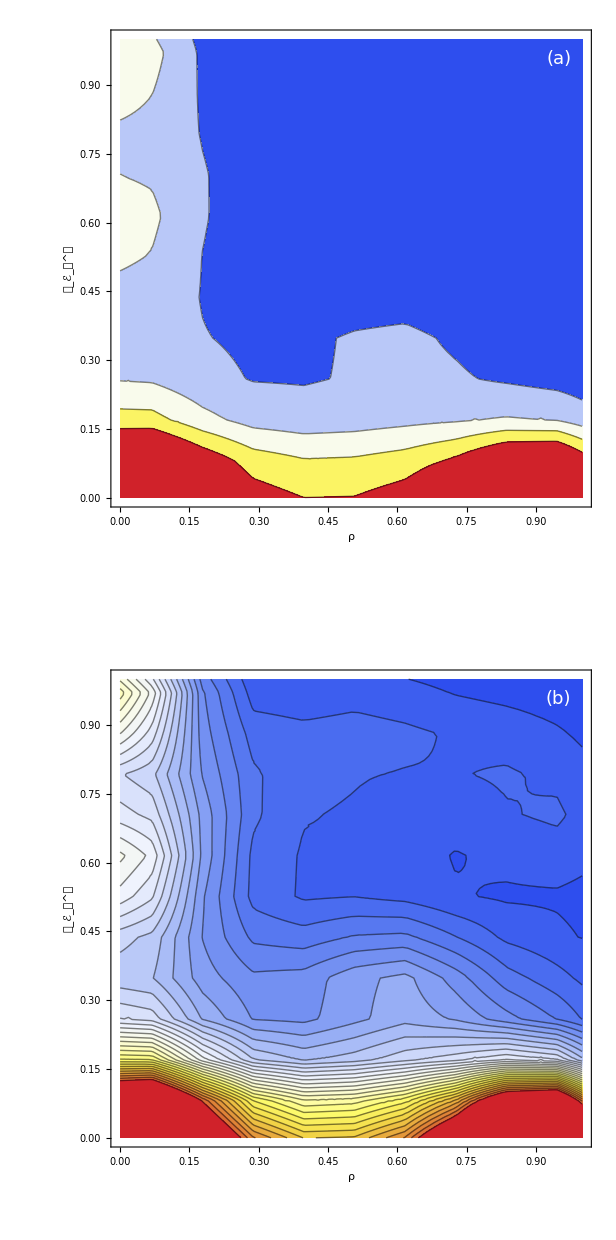

```mathematica
(*Creating Grids*)
row=GraphicsColumn[{ContourPlot[pdf,{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",Contours->4,ClippingStyle->Automatic,Epilog->Inset[Style["(a)",18,White],Offset[{-20,-20},Scaled[{1,1}]],{Right,Top}],Frame->True,FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},LabelStyle->Directive[FontFamily->"Helvetica",Black,FontSize->14],ImageSize->Large],
ContourPlot[pdf,{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",Contours->30,ClippingStyle->Automatic,Epilog->Inset[Style["(b)",18,White],Offset[{-20,-20},Scaled[{1,1}]],{Right,Top}],Frame->True,FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},LabelStyle->Directive[FontFamily->"Helvetica",Black,FontSize->14],ImageSize->Large]}];
Show[row]
```

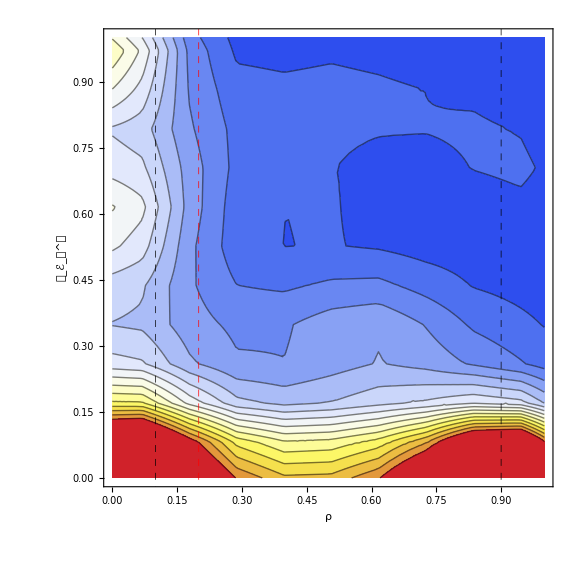

```mathematica
(*Generating contour plot *)contPlot= ContourPlot[pdf,{x,0,1},{y,0,1},GridLines->{{{0.2,Red},{0.1,Black},{0.9,Black}},None},GridLinesStyle->Directive[Red, Dashed,Thick],Contours->15,ClippingStyle->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},LabelStyle->Directive[FontFamily->"Helvetica",Black,FontSize->14],ImageSize->Large]
```

```mathematica
(*Training predictive function*)
predNet = Predict[trainTest[[1]],ValidationSet->trainTest[[2]]];
Information[predNet]
```

Predictor information
Data type | Numerical
Standard deviation | 0.361 ± 0.0079
Method | DecisionTree
Single evaluation time | 1.98 ms/example
Batch evaluation speed | 114. examples/ms
Loss | 0.398 ± 0.029
Model memory | 212. kB
Training examples used | 682 examples
Training time | 1.57 s
 |

```mathematica
GroupBy[cleanDat,First]//Length
```

111

```mathematica
predNet
```

PredictorFunction[…]

```mathematica
Plot[Table[PDF[predNet[y,"Distribution"],x],{y,0,1,0.1}],{x,0,1}]
```

$Aborted

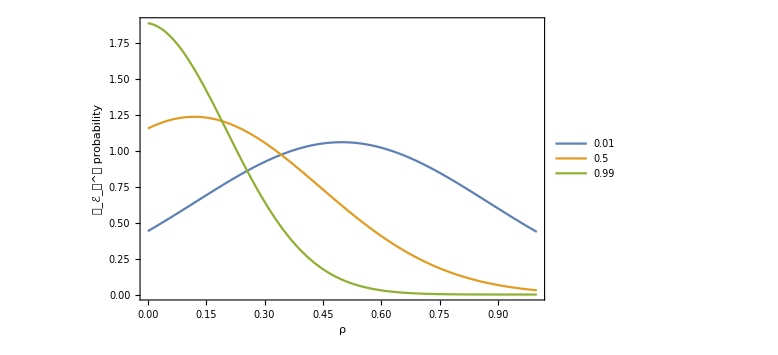

```mathematica
plot1 = Plot[{PDF[predNet[0.01,"Distribution"],x],PDF[predNet[0.5,"Distribution"],x],PDF[predNet[0.99,"Distribution"],x]},{x,0,1},PlotRange->All,Frame->True,FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥 probability"},LabelStyle->Directive[FontFamily->"Helvetica",Black,FontSize->14],PlotLegends->{"0.01","0.5","0.99"},ImageSize->Large]
```

```mathematica
Export["/Users/errust/Desktop/PredConf.png",%87,"PNG", ImageResolution->600,ImageSize->2000]
```

/Users/errust/Desktop/PredConf.png